x=3-2.5=0.5

y=ReLU(x) plot

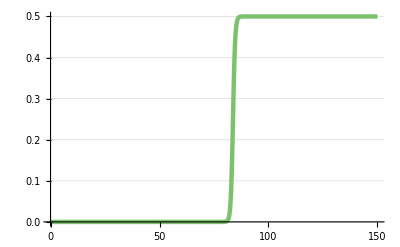

x=2-4=-2

y=ReLU(x) plot

-Graphics-

```mathematica
Get[NotebookDirectory[]<>"/relu.m"];

Print["x=3-2.5=0.5"];
xp0=3;xm0=2.5;
rsys=ReLURsys[xp0,xm0];
tmax=150;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys],tmax];
Print["y=ReLU(x) plot"]
PlotForPaper[{yp[t]-ym[t]}/.sol,tmax,25]

Print["x=2-4=-2"];
xp0=2;xm0=4;
rsys=ReLURsys[xp0,xm0];
tmax=150;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys],tmax];
Print["y=ReLU(x) plot"]
PlotForPaper[{yp[t]-ym[t]}/.sol,tmax,25]
```